Piecewise[{{(-((1-dt+(1+dt) Cos[k]) (2 (1+dt)^2 Cos[k] Sin[k]-2 (1+dt) (1-dt+(1+dt) Cos[k]) Sin[k]))/(2 ((1-dt+(1+dt) Cos[k])^2+(1+dt)^2 Sin[k]^2)^(3/2))-((1+dt) Sin[k])/(√((1-dt+(1+dt) Cos[k])^2+(1+dt)^2 Sin[k]^2)))/(√(1-(1-dt+(1+dt) Cos[k])^2/((1-dt+(1+dt) Cos[k])^2+(1+dt)^2 Sin[k]^2))), k<0}, {1/2 √((1+dt)^2), k==0}, {-(-((1-dt+(1+dt) Cos[k]) (2 (1+dt)^2 Cos[k] Sin[k]-2 (1+dt) (1-dt+(1+dt) Cos[k]) Sin[k]))/(2 ((1-dt+(1+dt) Cos[k])^2+(1+dt)^2 Sin[k]^2)^(3/2))-((1+dt) Sin[k])/(√((1-dt+(1+dt) Cos[k])^2+(1+dt)^2 Sin[k]^2)))/(√(1-(1-dt+(1+dt) Cos[k])^2/((1-dt+(1+dt) Cos[k])^2+(1+dt)^2 Sin[k]^2))), True}}]

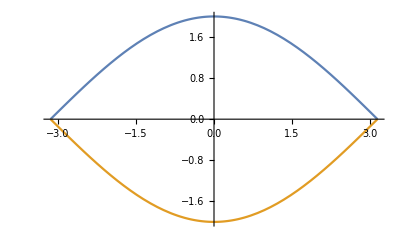

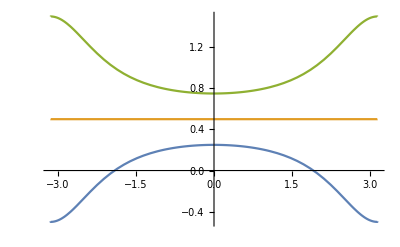

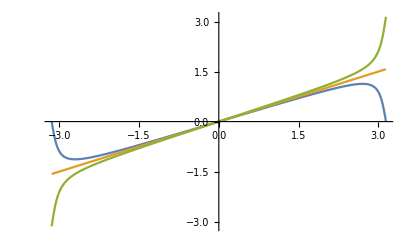

```mathematica
hx[dt_,k_]:=1-dt+(1+dt)*Cos[k];

hy[dt_,k_]:=(1+dt)*Sin[k];

h[dt_,k_]:=Sqrt[hx[dt,k]*hx[dt,k]+hy[dt,k]*hy[dt,k]];

coshalf[dt_,k_]:=Sqrt[1/2*(1+hx[dt,k]/h[dt,k])];
sinhalf[dt_,k_]:=Sqrt[1/2*(1-hx[dt,k]/h[dt,k])];

phi[dt_,k_]:=Piecewise[{{ArcCos[hx[dt,k]/h[dt,k]],k>0},{-ArcCos[hx[dt,k]/h[dt,k]],k≤0}}];

D[phi[dt,k],k]

dphi[dt_,k_]:=Piecewise[{{-((-(((1-dt+(1+dt) Cos[k]) (2 (1+dt)^2 Cos[k] Sin[k]-2 (1+dt) (1-dt+(1+dt) Cos[k]) Sin[k]))/(2 ((1-dt+(1+dt) Cos[k])^2+(1+dt)^2 Sin[k]^2)^(3/2)))-((1+dt) Sin[k])/Sqrt[(1-dt+(1+dt) Cos[k])^2+(1+dt)^2 Sin[k]^2])/Sqrt[1-(1-dt+(1+dt) Cos[k])^2/((1-dt+(1+dt) Cos[k])^2+(1+dt)^2 Sin[k]^2)]),k>0},{(-(((1-dt+(1+dt) Cos[k]) (2 (1+dt)^2 Cos[k] Sin[k]-2 (1+dt) (1-dt+(1+dt) Cos[k]) Sin[k]))/(2 ((1-dt+(1+dt) Cos[k])^2+(1+dt)^2 Sin[k]^2)^(3/2)))-((1+dt) Sin[k])/Sqrt[(1-dt+(1+dt) Cos[k])^2+(1+dt)^2 Sin[k]^2])/Sqrt[1-(1-dt+(1+dt) Cos[k])^2/((1-dt+(1+dt) Cos[k])^2+(1+dt)^2 Sin[k]^2)],k≤0}}];

Plot[{h[0, k], -h[0,k]},{k,-Pi, Pi}]

Plot[{dphi[-0.5,k],dphi[0,k],dphi[0.5,k]},{k,-Pi,Pi}]

Plot[{phi[-0.05,k],phi[0,k],phi[0.05,k]},{k,-Pi,Pi}]
```